# Spiral II

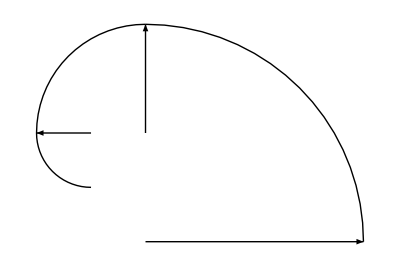

```mathematica
Graphics[{
Arrow[{{0,0},{1,0}}],Circle[{0,0},1,{0,π/2}],
Arrow[{{0,1/2},{0,1}}],Circle[{0,1/2},1/2,{π/2,π}],
Arrow[{{-1/4,1/2},{-1/2,1/2}}],Circle[{-1/4,1/2},1/4,{π ,3/2 π}]
}]
```

```mathematica
(* the step for the circle center *)
step[i_]:=1/2^i{-Cos[i π/2],Sin[i π/2]}
n[i_]:=Sum[step[j],{j,0,i}]+{1,0}+{-1/5,-2/5}
h[i_]:=Sum[step[j],{j,0,i}]+{1,0}+step[i]+{-1/5,-2/5}
(* step for arc angle *)
steparc[i_]:={π/2,π}-i π/2
```

```mathematica
Spiral=Table[{Line[
{n[i],
n[i]+step[i],
n[i]+2step[i+1]+step[i],n[i]+2step[i+1]+step[i]+4step[i+2]}
],
Circle[n[i],Norm[step[i]],steparc[i]]
},{i,-1,10}];
```

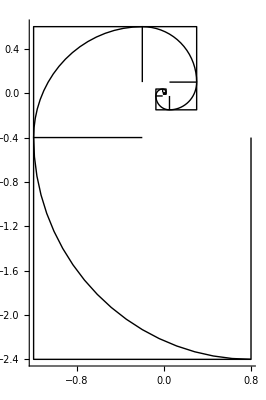

```mathematica
Graphics[Spiral,Axes->True]
```

```mathematica
ArcTan[(n[i][[2]]+step[i][[2]])/(n[i][[1]]+step[i][[1]])]/.{i->2}
% 180/π//N
```

ArcTan[1/3]

18.4349

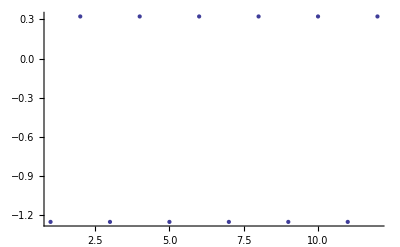

```mathematica
ListPlot[Table[ArcTan[(n[i][[2]]+step[i][[2]])/(n[i][[1]]+step[i][[1]])],{i,-1,10}]]
```

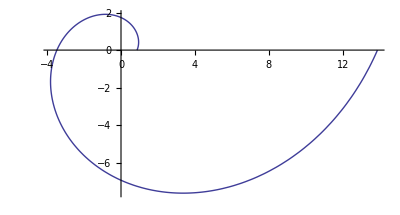

```mathematica
PolarPlot[2^((θ-ArcTan[1/3]) 2/π),{θ,0,2π}]
```